```mathematica
Tcm[ϵ_,λ_,μ_]:={{1-ϵ λ, μ},{-ϵ λ, μ}}
Tnag[ϵ_,λ_,μ_]:={{1-ϵ λ, μ(1-ϵ λ)},{-ϵ λ, μ(1-ϵ λ)}}
Tleap[ϵ_,λ_,μ_]:={{1-ϵ λ, μ^(1/2)(2-ϵ λ)},{-ϵ λ μ^(1/2), μ(1-ϵ λ)}}
(*Tleapalpha[ϵ_,λ_,μ_,α_]:={{1-ϵ λ, μ^(1/2)(1+α-ϵ λ)},{-ϵ λ μ^(1/2), μ(1-ϵ λ)}}*)
```

```mathematica
Eigenvalues[Tcm[ϵ,λ,μ]]
Eigenvalues[Tnag[ϵ,λ,μ]]
Eigenvalues[Tleap[ϵ,λ,μ]]
(*Eigenvalues[Tleapalpha[ϵ,λ,μ,α]]*)
```

{1/2 (1-ϵ λ-√((-1+ϵ λ-μ)^2-4 μ)+μ),1/2 (1-ϵ λ+√((-1+ϵ λ-μ)^2-4 μ)+μ)}

{1/2 (1-ϵ λ+μ-ϵ λ μ-√(-4 (μ-ϵ λ μ)+(-1+ϵ λ-μ+ϵ λ μ)^2)),1/2 (1-ϵ λ+μ-ϵ λ μ+√(-4 (μ-ϵ λ μ)+(-1+ϵ λ-μ+ϵ λ μ)^2))}

{1/2 (1-ϵ λ+μ-ϵ λ μ-√(-4 μ+(-1+ϵ λ-μ+ϵ λ μ)^2)),1/2 (1-ϵ λ+μ-ϵ λ μ+√(-4 μ+(-1+ϵ λ-μ+ϵ λ μ)^2))}

```mathematica
Solve[(-1+ϵ λ-μ)^2-4 μ==0,ϵ]
```

{{ϵ→(1-2 √μ+μ)/λ},{ϵ→(1+2 √μ+μ)/λ}}

```mathematica
1/2 (1-ϵ λ-√((-1+ϵ λ-μ)^2-4 μ)+μ)/.{ϵ->(1-2 √μ+μ)/λ}//FullSimplify
1/2 (1-ϵ λ-√((-1+ϵ λ-μ)^2-4 μ)+μ)/.{ϵ->(1+2 √μ+μ)/λ}//FullSimplify
```

√μ

-√μ

```mathematica
Solve[-4 (μ-ϵ λ μ)+(-1+ϵ λ-μ+ϵ λ μ)^2==0,ϵ]
```

{{ϵ→1/λ},{ϵ→(-1+μ)^2/(λ (1+μ)^2)}}

```mathematica
1/2 (1-ϵ λ+μ-ϵ λ μ-√(-4 (μ-ϵ λ μ)+(-1+ϵ λ-μ+ϵ λ μ)^2))/.{ϵ->(-1+μ)^2/(λ (1+μ)^2)}//FullSimplify
1/2 (1-ϵ λ+μ-ϵ λ μ-√(-4 (μ-ϵ λ μ)+(-1+ϵ λ-μ+ϵ λ μ)^2))/.{ϵ->1/λ}//FullSimplify
```

(2 μ)/(1+μ)

0

```mathematica
EigenCm1[ϵ_,λ_,μ_]:=1/2 (1-ϵ λ-√((-1+ϵ λ-μ)^2-4 μ)+μ)
EigenCm2[ϵ_,λ_,μ_]:=1/2 (1-ϵ λ+√((-1+ϵ λ-μ)^2-4 μ)+μ)


EigenNag1[ϵ_,λ_,μ_]:=1/2 (1-ϵ λ+μ-ϵ λ μ-√(-4 (μ-ϵ λ μ)+(-1+ϵ λ-μ+ϵ λ μ)^2))
EigenNag2[ϵ_,λ_,μ_]:=1/2 (1-ϵ λ+μ-ϵ λ μ+√(-4 (μ-ϵ λ μ)+(-1+ϵ λ-μ+ϵ λ μ)^2))

EigenLeap1[ϵ_,λ_,μ_]:=1/2 (1-ϵ λ+μ-ϵ λ μ-√(-4 μ+(-1+ϵ λ-μ+ϵ λ μ)^2))
EigenLeap2[ϵ_,λ_,μ_]:=1/2 (1-ϵ λ+μ-ϵ λ μ+√(-4 μ+(-1+ϵ λ-μ+ϵ λ μ)^2))

(*
EigenLeapAlpha1[ϵ_,λ_,μ_,α_]:=1/2 (1-ϵ λ+μ-ϵ λ μ-√((-1+ϵ λ-μ+ϵ λ μ)^2-4 (μ-ϵ λ μ+α ϵ λ μ)))
EigenLeapAlpha2[ϵ_,λ_,μ_,α_]:=1/2 (1-ϵ λ+μ-ϵ λ μ+√((-1+ϵ λ-μ+ϵ λ μ)^2-4 (μ-ϵ λ μ+α ϵ λ μ)))
*)
```

```mathematica
Manipulate[Show[
Graphics[{LightGray, Opacity[0.2],Disk[{0,0},1]}],
Graphics[Circle[{0,0},μ^(1/2)]],
Graphics[Circle[{μ/(1+μ),0},μ/(1+μ)]],
(******)
ListPlot[{{Re[EigenCm1[ϵ, λ, μ]],Im[EigenCm1[ϵ, λ, μ]]}},PlotStyle->Directive[Blue,PointSize[0.03]]],
ListPlot[{{Re[EigenCm2[ϵ, λ, μ]],Im[EigenCm2[ϵ, λ, μ]]}},
PlotStyle->Directive[Blue,PointSize[0.03]]],
(******)
ListPlot[{{Re[EigenNag1[ϵ, λ, μ]],Im[EigenNag1[ϵ, λ, μ]]}},PlotStyle->Directive[Green,PointSize[0.03]]],
ListPlot[{{Re[EigenNag2[ϵ, λ, μ]],Im[EigenNag2[ϵ, λ, μ]]}},
PlotStyle->Directive[Green,PointSize[0.03]]],
(******)
ListPlot[{{Re[EigenLeap1[ϵ, λ, μ]],Im[EigenLeap1[ϵ, λ, μ]]}},PlotStyle->Directive[Black,PointSize[0.03]]],
ListPlot[{{Re[EigenLeap2[ϵ, λ, μ]],Im[EigenLeap2[ϵ, λ, μ]]}},
PlotStyle->Directive[Black,PointSize[0.03]]],
(******)
AxesOrigin->{0,0},
AspectRatio->1,
PlotRange->{{-1.2,1.2},{-1.2,1.2}},
Frame->True
],{ϵ,0,3},{λ,1,2},{μ,0.5,1}]
```

```mathematica
MakeGraph[ϵ_,λ_,μ_]:=Show[
Graphics[{Gray, Opacity[0.2],Disk[{0,0},1]}],
Graphics[Circle[{0,0},μ^(1/2)]],
Graphics[Circle[{μ/(1+μ),0},μ/(1+μ)]],
(******)
ListPlot[{{Re[EigenCm1[ϵ, λ, μ]],Im[EigenCm1[ϵ, λ, μ]]}},PlotStyle->Directive[Blue,PointSize[0.04]],PlotLegends->Placed[{"CM"},Above]],
ListPlot[{{Re[EigenCm2[ϵ, λ, μ]],Im[EigenCm2[ϵ, λ, μ]]}},
PlotStyle->Directive[Blue,PointSize[0.04]]],
(******)
ListPlot[{{Re[EigenNag1[ϵ, λ, μ]],Im[EigenNag1[ϵ, λ, μ]]}},PlotStyle->Directive[Green,PointSize[0.04]],PlotLegends->Placed[{"NAG"},Above]],
ListPlot[{{Re[EigenNag2[ϵ, λ, μ]],Im[EigenNag2[ϵ, λ, μ]]}},
PlotStyle->Directive[Green,PointSize[0.04]]],
(******)
ListPlot[{{Re[EigenLeap1[ϵ, λ, μ]],Im[EigenLeap1[ϵ, λ, μ]]}},PlotStyle->Directive[Black,PointSize[0.04]],PlotLegends->Placed[{"Leap"},Above]],
ListPlot[{{Re[EigenLeap2[ϵ, λ, μ]],Im[EigenLeap2[ϵ, λ, μ]]}},
PlotStyle->Directive[Black,PointSize[0.04]]],
(******)
AxesOrigin->{0,0},
AspectRatio->1,
PlotRange->{{-1.2,1.2},{-1.2,1.2}},
Frame->True
]
```

```mathematica
g=GraphicsGrid[{{MakeGraph[0.5,1,0.8],MakeGraph[0.98,1,0.8],MakeGraph[1.38,1,0.8]}},BaselinePosition->Center]
```

-Graphics-

```mathematica
Export["/Users/gui/circles.pdf",g]
```

/Users/gui/circles.pdf

```mathematica
(* in phase space variables *)
```

```mathematica
Solve[-4 μ m^2+(-m-μ m+μ h^2 λ)^2==0,h]
```

{{h→-√(m/λ+m/(λ μ)-(2 m)/(λ √μ))},{h→√(m/λ+m/(λ μ)-(2 m)/(λ √μ))},{h→-√(m/λ+m/(λ μ)+(2 m)/(λ √μ))},{h→√(m/λ+m/(λ μ)+(2 m)/(λ √μ))}}

```mathematica
Tcm[γ_,h_,m_,λ_]:={{1-h^2 λ/m, h Exp[-γ h]/m},{-h λ, Exp[-γ h]}}
Tnag[γ_,h_,m_,λ_]:={{1-h^2 λ/m, Exp[-γ h]h(1-λ h^2/m)/m},{-h λ, Exp[-γ h](1-λ h^2/m)}}
Tleap[γ_,h_,m_,λ_]:={{1-h^2 λ/2/m, Exp[-γ h/2]h(2-h^2 λ/2/m)/m/2},{-h λ Exp[-γ h /2], Exp[-γ h](1-h^2 λ/2/m)}}
```

```mathematica
Eigenvalues[Tcm[γ,h,m,λ]]
Eigenvalues[Tnag[γ,h,m,λ]]
Eigenvalues[Tleap[γ,h,m,λ]]
```

{(ⅇ^(-h γ) (m+ⅇ^(h γ) m-ⅇ^(h γ) h^2 λ-√(-4 ⅇ^(h γ) m^2+(-m-ⅇ^(h γ) m+ⅇ^(h γ) h^2 λ)^2)))/(2 m),(ⅇ^(-h γ) (m+ⅇ^(h γ) m-ⅇ^(h γ) h^2 λ+√(-4 ⅇ^(h γ) m^2+(-m-ⅇ^(h γ) m+ⅇ^(h γ) h^2 λ)^2)))/(2 m)}

{(ⅇ^(-h γ) (m^4+ⅇ^(h γ) m^4-h^2 m^3 λ-ⅇ^(h γ) h^2 m^3 λ-m^3 √(m-h^2 λ) √(m-2 ⅇ^(h γ) m+ⅇ^(2 h γ) m-h^2 λ-2 ⅇ^(h γ) h^2 λ-ⅇ^(2 h γ) h^2 λ)))/(2 m^4),(ⅇ^(-h γ) (m^4+ⅇ^(h γ) m^4-h^2 m^3 λ-ⅇ^(h γ) h^2 m^3 λ+m^3 √(m-h^2 λ) √(m-2 ⅇ^(h γ) m+ⅇ^(2 h γ) m-h^2 λ-2 ⅇ^(h γ) h^2 λ-ⅇ^(2 h γ) h^2 λ)))/(2 m^4)}

{(ⅇ^(-h γ) (8 m^4+8 ⅇ^(h γ) m^4-4 h^2 m^3 λ-4 ⅇ^(h γ) h^2 m^3 λ-√(-256 ⅇ^(h γ) m^8+(-8 m^4-8 ⅇ^(h γ) m^4+4 h^2 m^3 λ+4 ⅇ^(h γ) h^2 m^3 λ)^2)))/(16 m^4),(ⅇ^(-h γ) (8 m^4+8 ⅇ^(h γ) m^4-4 h^2 m^3 λ-4 ⅇ^(h γ) h^2 m^3 λ+√(-256 ⅇ^(h γ) m^8+(-8 m^4-8 ⅇ^(h γ) m^4+4 h^2 m^3 λ+4 ⅇ^(h γ) h^2 m^3 λ)^2)))/(16 m^4)}

```mathematica
EigenCm1[γ_,h_,m_,λ_]:=(ⅇ^(-h γ) (m+ⅇ^(h γ) m-ⅇ^(h γ) h^2 λ-√(-4 ⅇ^(h γ) m^2+(-m-ⅇ^(h γ) m+ⅇ^(h γ) h^2 λ)^2)))/(2 m)
EigenCm2[γ_,h_,m_,λ_]:=(ⅇ^(-h γ) (m+ⅇ^(h γ) m-ⅇ^(h γ) h^2 λ+√(-4 ⅇ^(h γ) m^2+(-m-ⅇ^(h γ) m+ⅇ^(h γ) h^2 λ)^2)))/(2 m)
EigenNag1[γ_,h_,m_,λ_]:=(ⅇ^(-h γ) (m^4+ⅇ^(h γ) m^4-h^2 m^3 λ-ⅇ^(h γ) h^2 m^3 λ-m^3 √(m-h^2 λ) √(m-2 ⅇ^(h γ) m+ⅇ^(2 h γ) m-h^2 λ-2 ⅇ^(h γ) h^2 λ-ⅇ^(2 h γ) h^2 λ)))/(2 m^4)
EigenNag2[γ_,h_,m_,λ_]:=(ⅇ^(-h γ) (m^4+ⅇ^(h γ) m^4-h^2 m^3 λ-ⅇ^(h γ) h^2 m^3 λ+m^3 √(m-h^2 λ) √(m-2 ⅇ^(h γ) m+ⅇ^(2 h γ) m-h^2 λ-2 ⅇ^(h γ) h^2 λ-ⅇ^(2 h γ) h^2 λ)))/(2 m^4)
EigenLeap1[γ_,h_,m_,λ_]:=(ⅇ^(-h γ) (8 m^4+8 ⅇ^(h γ) m^4-4 h^2 m^3 λ-4 ⅇ^(h γ) h^2 m^3 λ-√(-256 ⅇ^(h γ) m^8+(-8 m^4-8 ⅇ^(h γ) m^4+4 h^2 m^3 λ+4 ⅇ^(h γ) h^2 m^3 λ)^2)))/(16 m^4)
EigenLeap2[γ_,h_,m_,λ_]:=(ⅇ^(-h γ) (8 m^4+8 ⅇ^(h γ) m^4-4 h^2 m^3 λ-4 ⅇ^(h γ) h^2 m^3 λ+√(-256 ⅇ^(h γ) m^8+(-8 m^4-8 ⅇ^(h γ) m^4+4 h^2 m^3 λ+4 ⅇ^(h γ) h^2 m^3 λ)^2)))/(16 m^4)
```

```mathematica
Manipulate[Show[
(******)
ListPlot[{{Re[EigenCm1[γ,h,m,λ]],Im[EigenCm1[γ,h,m,λ]]}},PlotStyle->Directive[Darker[Blue],PointSize[0.03]],Axes->True,PlotLegends->Placed[{"CM"},Above]],
ListPlot[{{Re[EigenCm2[γ,h,m,λ]],Im[EigenCm2[γ,h,m,λ]]}},
PlotStyle->Directive[Blue,PointSize[0.03]]],
(******)
ListPlot[{{Re[EigenNag1[γ,h,m,λ]],Im[EigenNag1[γ,h,m,λ]]}},PlotStyle->Directive[Green,PointSize[0.03]],PlotLegends->Placed[{"NAG"},Above]],
ListPlot[{{Re[EigenNag2[γ,h,m,λ]],Im[EigenNag2[γ,h,m,λ]]}},
PlotStyle->Directive[Green,PointSize[0.03]]],
(******)
ListPlot[{{Re[EigenLeap1[γ,h,m,λ]],Im[EigenLeap1[γ,h,m,λ]]}},PlotStyle->Directive[Black,PointSize[0.03]],PlotLegends->Placed[{"Leap"},Above]],
ListPlot[{{Re[EigenLeap2[γ,h,m,λ]],Im[EigenLeap2[γ,h,m,λ]]}},
PlotStyle->Directive[Black,PointSize[0.03]]],
(******)
Graphics[{Gray, Opacity[0.2],Disk[{0,0},1]}],
Graphics[Circle[{0,0},Exp[-γ h /2]]],
Graphics[Circle[{Exp[-γ h]/(1+Exp[-γ h]),0},Exp[-γ h]/(1+Exp[-γ h])]],
(*******)
AxesOrigin->{0,0},
AspectRatio->1,
PlotRange->{{-1.2,1.2},{-1.2,1.2}}
(*Frame->True*)
],{γ,0,1},{h,0,2},{m,1,2},{λ,1,2}]
```

```mathematica
ps=0.05;
MakePlot[γ_,h_,m_,λ_]:=Show[
Graphics[{Gray, Opacity[0.2],Disk[{0,0},1]},Axes->True],
(******)
ListPlot[{{Re[EigenCm1[γ,h,m,λ]],Im[EigenCm1[γ,h,m,λ]]}},PlotStyle->Directive[Blue,PointSize[ps]],Axes->True(*PlotLegends->Placed[{"CM"},Above]*)],
ListPlot[{{Re[EigenCm2[γ,h,m,λ]],Im[EigenCm2[γ,h,m,λ]]}},
PlotStyle->Directive[Blue,PointSize[ps]]],
(******)
ListPlot[{{Re[EigenNag1[γ,h,m,λ]],Im[EigenNag1[γ,h,m,λ]]}},PlotStyle->Directive[Green,PointSize[ps]](*PlotLegends->Placed[{"NAG"},Above]*)],
ListPlot[{{Re[EigenNag2[γ,h,m,λ]],Im[EigenNag2[γ,h,m,λ]]}},
PlotStyle->Directive[Green,PointSize[ps]]],
(******)
ListPlot[{{Re[EigenLeap1[γ,h,m,λ]],Im[EigenLeap1[γ,h,m,λ]]}},PlotStyle->Directive[Black,PointSize[ps]](*PlotLegends->Placed[{"Leap"},Above]*)],
ListPlot[{{Re[EigenLeap2[γ,h,m,λ]],Im[EigenLeap2[γ,h,m,λ]]}},
PlotStyle->Directive[Black,PointSize[ps]]],
(******)
Graphics[Circle[{0,0},Exp[-γ h /2]]],
Graphics[Circle[{Exp[-γ h]/(1+Exp[-γ h]),0},Exp[-γ h]/(1+Exp[-γ h])]],
(*******)
AxesOrigin->{0,0},
AspectRatio->1,
PlotRange->{{-1.1,1.1},{-1.1,1.1}}
]
```

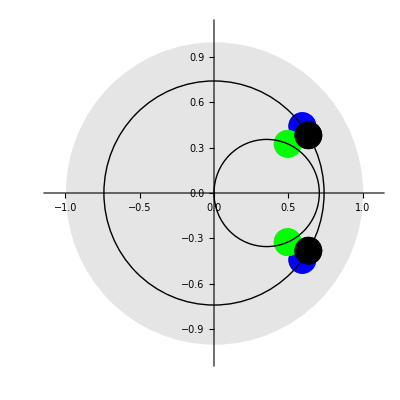

```mathematica
g1 = MakePlot[1, 0.6, 1, 1]
```

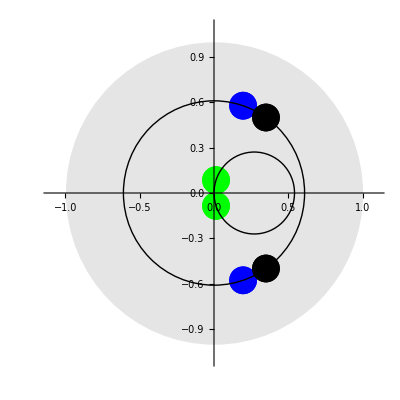

```mathematica
g2=MakePlot[1,0.99,1,1]
```

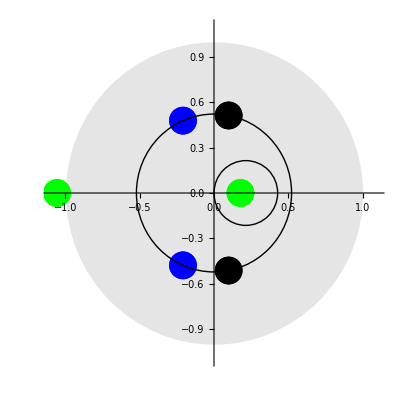

```mathematica
g3=MakePlot[1,1.3,1,1]
```

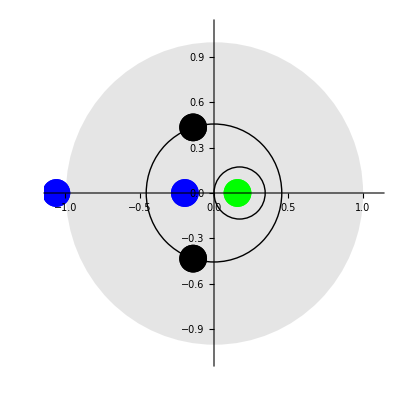

```mathematica
g4=MakePlot[1,1.57,1,1]
```

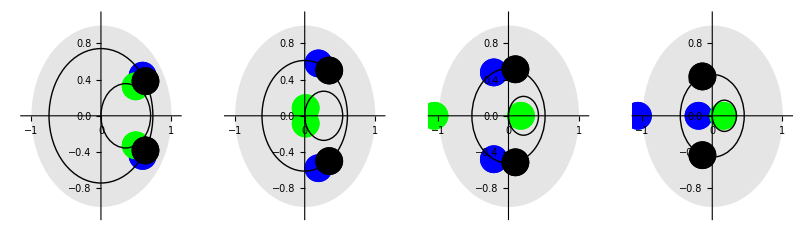

```mathematica
g=GraphicsGrid[{{g1,g2,g3,g4}},ImageSize->{800,240}]
```

```mathematica
Export["/Users/gui/my_papers/symplectic_relativistic_Neurips2020/circles.pdf",g]
```

/Users/gui/my_papers/symplectic_relativistic_Neurips2020/circles.pdf

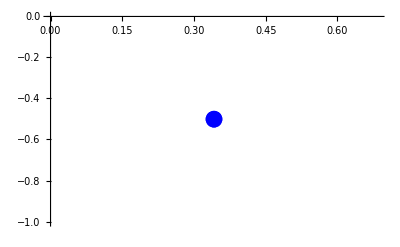

```mathematica
ListPlot[{{Re[EigenLeap1[1,1,1,1]],Im[EigenLeap1[1,1,1,1]]}},PlotStyle->Directive[Blue,PointSize[0.03]]]
```

```mathematica
Solve[(μ (m+μ m-μ h^2 λ-√(-4 μ m^2+(-m-μ m+μ h^2 λ)^2)))/(2 m)==-1,h]
```

{{h→-(√m √(1+μ+μ^2+μ^3))/(√λ μ)},{h→(√m √(1+μ+μ^2+μ^3))/(√λ μ)}}

```mathematica
(ⅇ^(-h γ) (m+ⅇ^(h γ) m-ⅇ^(h γ) h^2 λ-√(-4 ⅇ^(h γ) m^2+(-m-ⅇ^(h γ) m+ⅇ^(h γ) h^2 λ)^2)))/(2 m)
```

```mathematica
Solve[(μ (m^4+μ m^4-h^2 m^3 λ-μ h^2 m^3 λ-m^3 √(m-h^2 λ) √(m-2 μ m+μ^2 m-h^2 λ-2 μ h^2 λ-μ^2 h^2 λ)))/(2 m^4)==-1,h]
```

{{h→-(√m √(1+μ+μ^2+μ^3))/(√λ √μ √(1+μ+μ^2))},{h→(√m √(1+μ+μ^2+μ^3))/(√λ √μ √(1+μ+μ^2))}}

```mathematica
Solve[(μ (8 m^4+8 μ m^4-4 h^2 m^3 λ-4 μ h^2 m^3 λ-√(-256 μ m^8+(-8 m^4-8 μ m^4+4 h^2 m^3 λ+4 μ h^2 m^3 λ)^2)))/(16 m^4)==-1,h]
```

{{h→-(√2 √(m+m μ+m μ^2+m μ^3))/(√(λ μ+λ μ^2))},{h→(√2 √(m+m μ+m μ^2+m μ^3))/(√(λ μ+λ μ^2))}}

```mathematica
1+μ+μ^2+μ^3//FullSimplify
```

(1+μ) (1+μ^2)

```mathematica
1+μ+μ^2//FullSimplify
```

1+μ+μ^2

```mathematica
Solve[1+μ+μ^2==0,μ]
```

{{μ→-(-1)^(1/3)},{μ→(-1)^(2/3)}}